## Prepare

```mathematica
imgsize=700;
imgpadding={{70, 20}, {50, 10}};
```

Always use the first element in the vector to be the component of small eigenvalue.

```mathematica
$MachinePrecision
```

15.9546

### Modules

Making Plots

```mathematica
pltNorm[sol_,c1_,c2_,start_,end_]:=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2[x]]^2/.sol[[1]]],{x,start,end},PlotRange->All,ImageSize->imgsize,Frame->True];
```

Plot transitioin Probabilities: Probability of c2

```mathematica
pltProb[sol_,c2_,c1_,start_,end_,pltLabel_,frameLabel_]:=Plot[Evaluate[Abs[c2[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.sol[[1]]],{x,start,end},PlotRange->All,PlotLabel->pltLabel,ImageSize->imgsize,Frame->True,FrameLabel->frameLabel,ImagePadding->imgpadding,PerformanceGoal->"Quality"];
```

Rotation matrices

Rotation from vacuum to instantaneous matter basis

```mathematica
vac2instRotation[a0_,a1_,tv_]:=Module[{thetaxConst,alpha0=a0,alpha1=a1,thetav=tv},thetaxConst=ArcSin[Sin[2thetav]/(√(1+(alpha0+alpha1)^2-2(alpha0+alpha1)Cos[2thetav]))]/2;{{Cos[thetav-thetaxConst],-Sin[thetav-thetaxConst]},{Sin[thetav-thetaxConst],Cos[thetav-thetaxConst]}}]
```

Pauli matrices

```mathematica
sigma3=PauliMatrix[3];
sigma1=PauliMatrix[1];
```

Conversion from length (km) to energy (eV): 197.33 MeV*fm=1 =>

```mathematica
hbarc=197.33;
```

```mathematica
km2eV[km_]:=Module[{length=km},(hbarc*10^6)/(km*10^(18))]
eV2km[eV_]:=Module[{energy=eV},(hbarc*10^(-18))/(eV*10^(-6))]
```

#### Paramters

Paramters are grabbed from Kneller’s paper

#### Initial Condition

In (averaged) matter basis

```mathematica
θv=0.573;
energy=20*10^6; (* eV *)
deltam2=3*10^(-3); (* eV^2 *)
(* The following are calculated *)
omegav=deltam2/(2energy); (* 7.5*10^(-11) *) (*eV, delta^2m= 3*10^(-3)eV^2, E =20MeV*)
(* α0=Cos[2θv] *)
α0=Cos[2θv]/2;
(*  α1=0 *) α1=0.1α0;
(*β=0.937*)(* β=(2*km2eV[5.2533])/omegav *)
phasem=0;
```

```mathematica
β=(2*km2eV[5.27])/omegav
```

0.998507

The initial condition in matter basis

```mathematica
initAM={1,0}
```

{1,0}

Rotate to vacuum eigenbasis

```mathematica
initVacEigen=Transpose[vac2instRotation[α0,α1,θv]].{1,0};
vac2instRotation[α0,0,θv]//MatrixForm
(* initVac=initVacEigen *)
initVac=Transpose[vac2instRotation[α0,0,θv]].initAM
```

(0.994885 | 0.101012
-0.101012 | 0.994885)

{0.994885,0.101012}

```mathematica
endpoint= omegav/km2eV[10^4];
%//N
```

3800.74

#### Test of Defined Functions and Parametser + Check Numbers

```mathematica
"σ3 is "MatrixForm@sigma3
"σ1 is "MatrixForm@sigma1
```

σ3 is  (1 | 0
0 | -1)

σ1 is  (0 | 1
1 | 0)

Test Rotation

```mathematica
vac2instRotationTest=Module[{θv=ArcSin@√0.307},Grid[{{"Zero Matter Potential: "<>ToString@vac2instRotation[0,0,θv]},{"MSW Resonance: "<>ToString@vac2instRotation[Cos[2*θv],0,θv]}}]]
```

Zero Matter Potential: {{1., 0.}, {0., 1.}}
MSW Resonance: {{0.980433, 0.196852}, {-0.196852, 0.980433}}

Test Unit convsersion

```mathematica
km2eV[10^(-18)]
eV2km[10^6]
```

1.9733×10^8

1.9733×10^-16

#### Check Numbers

```mathematica
ArcSin[Sin[2θv]/(√(1+(α0+α1)^2-2(α0+α1)Cos[2θv]))]/2
Sin[2ArcTan[Sin[2θv]/(Cos[2θv]-α0)]/2]^2
```

0.684994

0.951337

```mathematica
omegav//N
```

7.5×10^-11

```mathematica
(6/omegav)*10^(-7)*197/Pi//N
```

501656.

```mathematica
1/km2eV[1]//N
```

5.06765×10^9

```mathematica
θv*Pi/180
```

0.0100007

```mathematica
(2Pi/omegav*√(1+α0^2-2α0 Cos[2θv]))*10^(-7)*197
```

1.54168×10^6

```mathematica
(100/omegav)*10^(-7)*197//N
```

2.62667×10^7

### Some Conversions and Comparisons

#### A Table of All Parameters

```mathematica
Grid[{{"-","θ_V","Δm^2/eV^2","E/MeV","ω_V/eV","λ_m/km","C_*","Phase of Matter Profiles"},{"Kneller",0.573,N@3*10^(-3),20,N@3*10^(-3)/(2*20*10^6),5.27,0.1,"η"},{"Now",θv,N@deltam2,N@energy*10^(-6),N@omegav,eV2km[β omegav/2],α1/α0,phasem}},Frame->All]
```

- | θ_V | Δm^2/eV^2 | E/MeV | ω_V/eV | λ_m/km | C_* | Phase of Matter Profiles
Kneller | 0.573 | 0.003 | 20 | 7.5×10^-11 | 5.27 | 0.1 | η
Now | 0.573 | 0.003 | 20. | 7.5×10^-11 | 5.27 | 0.1 | 0

#### Numerical Check

Frequencies/wavelength in Kneller’s paper

Vacuum

```mathematica
N@omegav
```

7.5×10^-11

Vacuum Wavelegth to km (Using Kneller’s convention that wavelength=2/)

```mathematica
eV2km[omegav]*2
```

5.26213

Matter frequency

```mathematica
omegam=omegav*√(α0^2+1-2α0 Cos[2θv])
```

7.00601×10^-11

Corresponding wavelength

```mathematica
eV2km[omegam]*2
```

5.63316

Wavelength of transition probability in Kneller’s resonance

```mathematica
(6*10^9/5)*10^(-5)
```

12000

This corresponds to many vacuum lengths

```mathematica
%/(eV2km[omegav]*2)
```

2280.44

## Equation Solving

### Sovling Schrodinger equation Hamiltonian

The normalized Hamiltonian in vacuum basis is

```mathematica
hamilVac[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*Sin[beta*x+phasem]},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

```mathematica
hamilVac[α0,α1,β,x]
```

{{-0.5+0.206068 (0.206068+0.0206068 Sin[0.998507 x]),0.+0.455561 (0.206068+0.0206068 Sin[0.998507 x])},{0.+0.455561 (0.206068+0.0206068 Sin[0.998507 x]),0.5-0.206068 (0.206068+0.0206068 Sin[0.998507 x])}}

```mathematica
waveVac0[x_]={waveVac01[x],waveVac02[x]};
solVac0=NDSolve[{I D[waveVac0[x],x]==hamilVac[α0,α1,β,x].waveVac0[x],waveVac0[0]==initVac},waveVac0[x],{x,0,endpoint}]
```

{{waveVac01[x]→InterpolatingFunction[{{0., 3800.74}}, <>][x],waveVac02[x]→InterpolatingFunction[{{0., 3800.74}}, <>][x]}}

```mathematica
solVac0Convergence=Assuming[waveVac02[x]∈Complexes,NDSolve[{I D[waveVac0[x],x]==hamilVac[α0,α1,β,x].waveVac0[x],waveVac0[0]==initVac},waveVac0[x],{x,0,endpoint},Method->"StiffnessSwitching"]]
```

{{waveVac01[x]→InterpolatingFunction[{{0., 3800.74}}, <>][x],waveVac02[x]→InterpolatingFunction[{{0., 3800.74}}, <>][x]}}

```mathematica
Plot[Evaluate[Abs[waveVac01[x]]^2+Abs[waveVac02[x]]^2/.{solVac0[[1]],solVac0Convergence[[1]]}],{x,0,endpoint},PlotStyle->{Blue,Red},PlotRange->All,ImageSize->imgsize,Frame->True];
```

```mathematica
pltNorm[solVac0,waveVac01,waveVac02,0,endpoint];
```

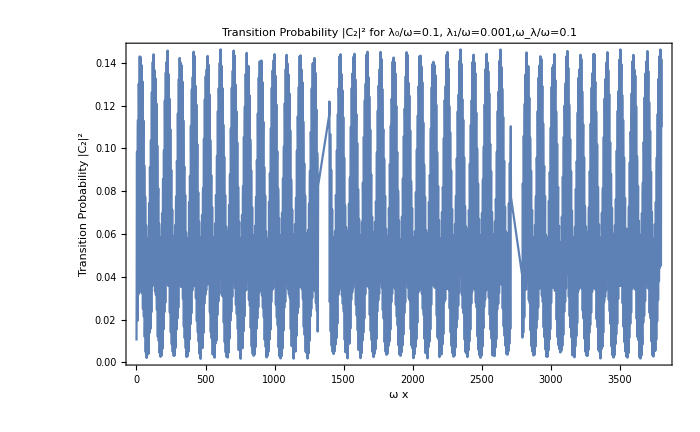

```mathematica
pltProb[solVac0,waveVac02,waveVac01,0,endpoint,"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",{"ω x","Transition Probability |C_2|^2"}]
```

The Imaginary Part

```mathematica
Grid[{{Plot[Evaluate[Im[waveVac01[x]]]/.solVac0[[1]],{x,0,endpoint},PlotRange->All,PlotLabel->"Imaginary Part of C_1 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Imaginary Part of C_1"},ImagePadding->imgpadding],
Plot[Evaluate[Re[waveVac01[x]]]/.solVac0[[1]],{x,0,endpoint},PlotRange->All,PlotLabel->"Re Part of C_1 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Real Part of C_1^2"},ImagePadding->imgpadding]},
{Plot[Evaluate[Im[waveVac02[x]]]/.solVac0[[1]],{x,0,endpoint},PlotRange->All,PlotLabel->"Imaginary Part of C_2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Imaginary Part of C_2"},ImagePadding->imgpadding],
Plot[Evaluate[Re[waveVac02[x]]]/.solVac0[[1]],{x,0,endpoint},PlotRange->All,PlotLabel->"Real Part of C_2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Real Part of C_2"},ImagePadding->imgpadding]}}];
```

### Solving in Vacuum Basis then Rotate

This problem can be solved in matter basis,hw

```mathematica
eqn1= I c1'[x]==Cos[2θv]/2(α0+α1 Cos[β x])c1[x]+Sin[2θv]/2(α0+α1 Cos[β x])c2[x]Exp[-I x]
eqn2=I c2'[x]==-Cos[2θv]/2(α0+α1 Cos[β x])c2[x]+ Sin[2θv]/2(α0+α1 Cos[β x])c1[x] Exp[I x]
```

ⅈ c1'[x]==0.206068 c1[x] (0.206068+0.0206068 Cos[0.998507 x])+0.455561 ⅇ^(-ⅈ x) c2[x] (0.206068+0.0206068 Cos[0.998507 x])

ⅈ c2'[x]==0.455561 ⅇ^(ⅈ x) c1[x] (0.206068+0.0206068 Cos[0.998507 x])-0.206068 c2[x] (0.206068+0.0206068 Cos[0.998507 x])

```mathematica
solVac=NDSolve[{eqn1,eqn2,c1[0]==initVac[[1]],c2[0]==initVac[[2]]},{c1,c2},{x,0,endpoint}]
```

{{c1→InterpolatingFunction[{{0., 3800.74}}, <>],c2→InterpolatingFunction[{{0., 3800.74}}, <>]}}

Check normalization

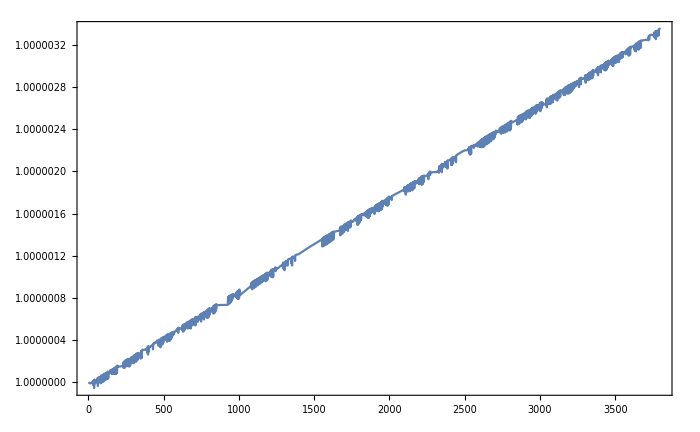

```mathematica
normVac=pltNorm[solVac,c1,c2,0,endpoint]
```

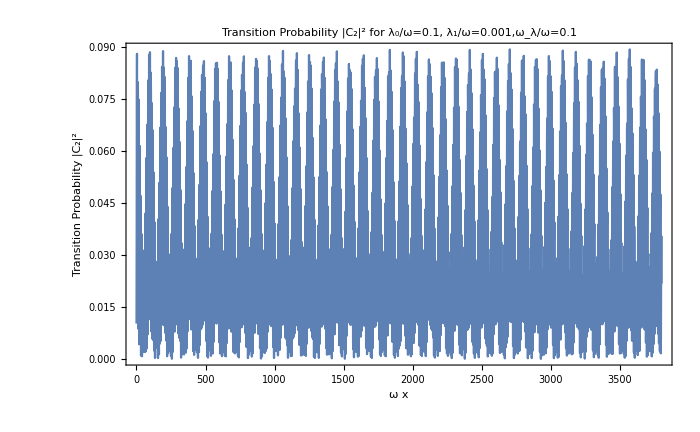

```mathematica
pltProb[solVac,c2,c1,0,endpoint,"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",{"ω x","Transition Probability |C_2|^2"}]
```

### Matter Basis

Wavefunction in matter basis is

```mathematica
instWaveFunction[x_]=vac2instRotation[α0,0,θv].{waveVac01[x],waveVac02[x]}/.solVac0[[1]]
```

{0.101012 InterpolatingFunction[{{0., 3800.74}}, <>][x]+0.994885 InterpolatingFunction[{{0., 3800.74}}, <>][x],0.994885 InterpolatingFunction[{{0., 3800.74}}, <>][x]-0.101012 InterpolatingFunction[{{0., 3800.74}}, <>][x]}

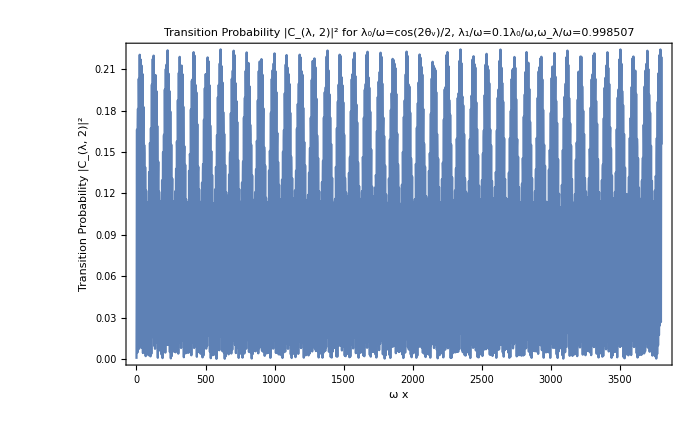

```mathematica
probInstHeavy=Plot[Abs[instWaveFunction[x][[2]]]^2/(Abs[instWaveFunction[x][[1]]]^2+Abs[instWaveFunction[x][[2]]]^2),{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

### Flavor Basis

```mathematica
instWaveFunction[x_]={{Cos[θv],Sin[θv]},{-Sin[θv],Cos[θv]}}.{waveVac01[x],waveVac02[x]}/.solVac0[[1]]
```

{0.542155 InterpolatingFunction[{{0., 3800.74}}, <>][x]+0.840278 InterpolatingFunction[{{0., 3800.74}}, <>][x],0.840278 InterpolatingFunction[{{0., 3800.74}}, <>][x]-0.542155 InterpolatingFunction[{{0., 3800.74}}, <>][x]}

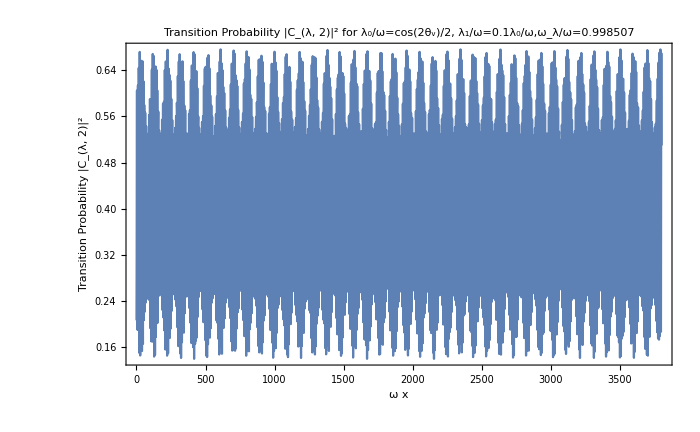

```mathematica
probInstHeavy=Plot[Abs[instWaveFunction[x][[2]]]^2/(Abs[instWaveFunction[x][[2]]]^2+Abs[instWaveFunction[x][[1]]]^2),{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

## Calculate in Matter Basis Directly

The calculation can be done in averaged matter basis directly.

Hamiltonian in (averaged) Matter basis is

```mathematica
hamilAM[alpha0_,alpha1_,beta_,x_]:=vac2instRotation[α0,0,θv].hamilVac[alpha0,alpha1,beta,x].Transpose[vac2instRotation[α0,0,θv]]//FullSimplify
```

Test this function

```mathematica
hamilAM[α0,α1,β,x]
```

{{-0.429331+0.00604656 Sin[0.998507 x],0.183921+0.00834258 Sin[0.998507 x]},{0.183921+0.00834258 Sin[0.998507 x],0.429331-0.00604656 Sin[0.998507 x]}}

System to be solved is the Schrodinger equation

```mathematica
waveAM[x_]={waveAM1[x],waveAM2[x]};
```

```mathematica
solAM=NDSolve[{I D[waveAM[x],x]==hamilAM[α0,α1,β,x].waveAM[x],waveAM[0]==initAM},waveAM[x],{x,0,endpoint}];
```

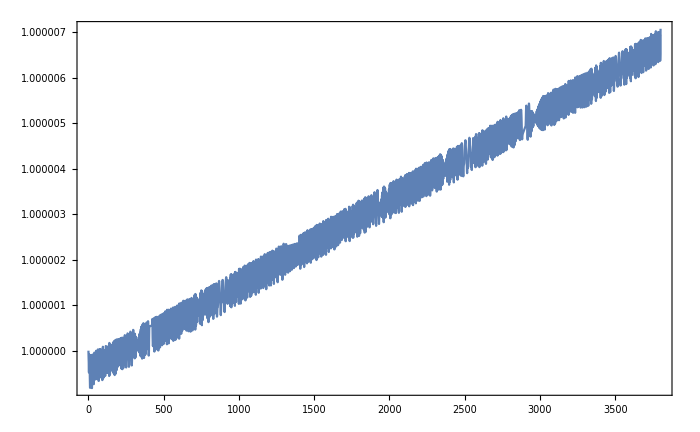

```mathematica
pltNorm[solAM,waveAM1,waveAM2,0,endpoint]
```

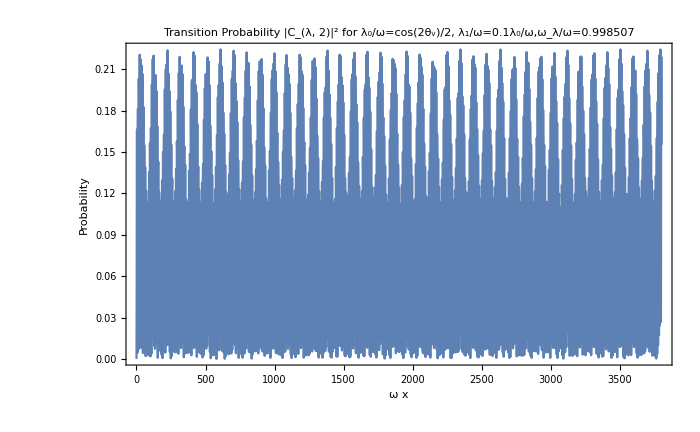

```mathematica
pltProb[solAM,waveAM2,waveAM1,0,endpoint,"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],{"ω x","Probability"}]
```

### Scanning Parameters

```mathematica
Manipulate[pltProb[NDSolve[{I D[waveAM[x],x]==hamilAM[α0,α1,beta,x].waveAM[x],waveAM[0]==initAM},waveAM[x],{x,0,endpoint}],waveAM2,waveAM1,0,endpoint,"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[beta],{"ω x","Probability"}],{beta,0.7,If[wide,5,1.0],0.01},{{wide,False,"Wide Range"},{False,True}}]
```

## Stimulated?

```mathematica
adiabProb[thetavA_,alpha0A_,alpha1A_,betaA_,xA_]:=((Sin[thetavA]^2)( Sin[xA/2]^2))/((alpha0A+alpha1A*Sin[betaA*xA])^2+1-2(alpha0A+alpha1A*Sin[betaA*xA])Cos[2thetavA])
```

```mathematica
adiabDeno[thetavA_,omegavA_,alpha0A_,alpha1A_,betaA_,xA_]:=(alpha0A+alpha1A*Sin[betaA*xA])^2+1-2(alpha0A+alpha1A*Sin[betaA*xA])Cos[2thetavA]
```

```mathematica
vacOscProb[thetavA_,omegavA_,xA_]:=(Sin[thetavA]^2)( Sin[xA/2]^2)
```

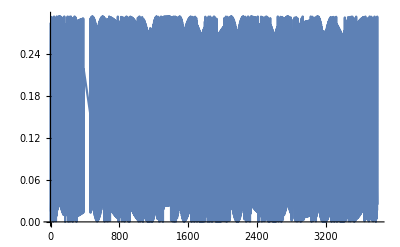

```mathematica
Plot[vacOscProb[θv,omegav,x],{x,0,endpoint}]
```

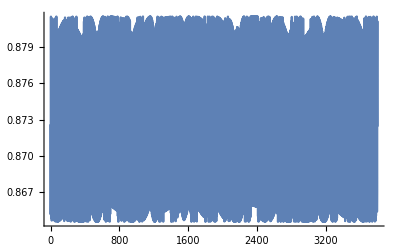

```mathematica
Plot[adiabDeno[θv,omegav,α0,α1,β,x],{x,0,endpoint}]
```

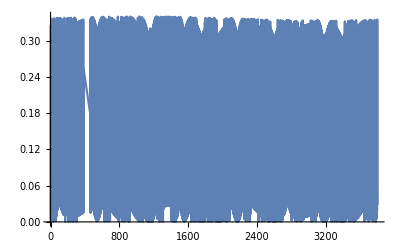

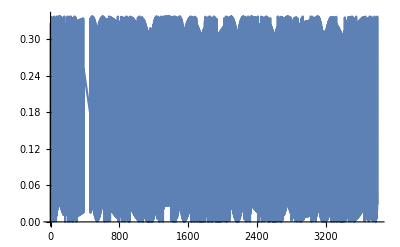

```mathematica
Plot[adiabProb[θv,α0,α1,β,x],{x,0,endpoint}]
Plot[adiabProb[θv,α0,0,β,x],{x,0,endpoint}]
```

## Temp

```mathematica
{{Cos[tv],-Sin[tv]},{Sin[tv],Cos[tv]}}.{{Cos[tm],Sin[tm]},{-Sin[tm],Cos[tm]}}//FullSimplify//MatrixForm
```

(Cos[tm-tv] | Sin[tm-tv]
-Sin[tm-tv] | Cos[tm-tv])